```mathematica
ClearAll["Global`*"]
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]
```

```mathematica
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-L IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]
```

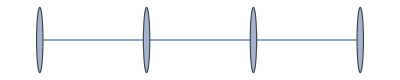

{1/2 (-1-√5),1/2 (1+√5),1/2 (1-√5),1/2 (-1+√5)}

{{1/L,1/L,0},{1/L,1/L,1},{0,1,0}}

{{2/(-1-√5),2/(-1-√5),0},{2/(-1-√5),2/(-1-√5),1},{0,1,0}}

{1/2 (-1-√5),(-1+√5+√(22-2 √5))/(2 (1+√5)),(-1+√5-√(22-2 √5))/(2 (1+√5))}

{{((1+√5) ⅇ^(-(ⅈ (3+√5) t)/(1+√5)))/(2 (3+2 √5))+((√(22-2 √5)+√5 (4+√(22-2 √5))) ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))+((√(22-2 √5)+√5 (-4+√(22-2 √5))) ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)),(2 ⅇ^(-(ⅈ (3+√5) t)/(1+√5)))/(-1+3 √5)+(2 (-1+√5-√(22-2 √5)) ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))-(2 (-1+√5+√(22-2 √5)) ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)),2 (1+√5) (-ⅇ^(-(ⅈ (3+√5) t)/(1+√5))/(12+8 √5)+(2 ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))-(2 ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)))},{(2 ⅇ^(-(ⅈ (3+√5) t)/(1+√5)))/(-1+3 √5)+(2 (-1+√5-√(22-2 √5)) ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))-(2 (-1+√5+√(22-2 √5)) ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)),((2+√5) ⅇ^(-(ⅈ (3+√5) t)/(1+√5)))/(3+2 √5)+((-12+√(110-10 √5)+√(22-2 √5)) ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))+((12+√(110-10 √5)+√(22-2 √5)) ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)),1/2 (1+√5) (-(2 (1+√5) ⅇ^(-(ⅈ (3+√5) t)/(1+√5)))/(12+8 √5)-(2 (3+√5-√(22-2 √5)) ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))+(2 (3+√5+√(22-2 √5)) ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)))},{2 (1+√5) (-ⅇ^(-(ⅈ (3+√5) t)/(1+√5))/(12+8 √5)+(2 ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))-(2 ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5))),1/2 (1+√5) (-(2 (1+√5) ⅇ^(-(ⅈ (3+√5) t)/(1+√5)))/(12+8 √5)-(2 (3+√5-√(22-2 √5)) ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))+(2 (3+√5+√(22-2 √5)) ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5))),((1+√5) ⅇ^(-(ⅈ (3+√5) t)/(1+√5)))/(2 (3+2 √5))+((√(110-10 √5)+3 √(22-2 √5)-2 (5+√5)) ⅇ^(-(ⅈ (1-√5+√(22-2 √5)) t)/(2 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))+((√(110-10 √5)+3 √(22-2 √5)+2 (5+√5)) ⅇ^((ⅈ (-1+√5+√(22-2 √5)) t)/(2 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5))}}

{{(ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))) (400+164 √5-33 √(110-10 √5)-77 √(22-2 √5)+(400+164 √5+33 √(110-10 √5)+77 √(22-2 √5)) ⅇ^((ⅈ √(1/2 (11-√5)) π)/(1+√5))+4 (59+21 √5) ⅇ^((ⅈ (5+3 √5+√(22-2 √5)) π)/(4 (1+√5)))))/(4 (259+103 √5)),(2 ⅇ^((ⅈ (3+√5) π)/(2 (1+√5))))/(-1+3 √5)+(2 (-1+√5-√(22-2 √5)) ⅇ^((ⅈ (1-√5+√(22-2 √5)) π)/(4 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))-(2 (-1+√5+√(22-2 √5)) ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)),2 (1+√5) (-ⅇ^((ⅈ (3+√5) π)/(2 (1+√5)))/(12+8 √5)+(2 ⅇ^((ⅈ (1-√5+√(22-2 √5)) π)/(4 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))-(2 ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)))},{(2 ⅇ^((ⅈ (3+√5) π)/(2 (1+√5))))/(-1+3 √5)+(2 (-1+√5-√(22-2 √5)) ⅇ^((ⅈ (1-√5+√(22-2 √5)) π)/(4 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))-(2 (-1+√5+√(22-2 √5)) ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)),((2+√5) ⅇ^((ⅈ (3+√5) π)/(2 (1+√5))))/(3+2 √5)+((-12+√(110-10 √5)+√(22-2 √5)) ⅇ^((ⅈ (1-√5+√(22-2 √5)) π)/(4 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))+((12+√(110-10 √5)+√(22-2 √5)) ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)),1/2 (1+√5) (-((1+√5) ⅇ^((ⅈ (3+√5) π)/(2 (1+√5))))/(6+4 √5)-(2 (3+√5-√(22-2 √5)) ⅇ^((ⅈ (1-√5+√(22-2 √5)) π)/(4 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))+(2 (3+√5+√(22-2 √5)) ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5)))},{2 (1+√5) (-ⅇ^((ⅈ (3+√5) π)/(2 (1+√5)))/(12+8 √5)+(2 ⅇ^((ⅈ (1-√5+√(22-2 √5)) π)/(4 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))-(2 ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5))),1/2 (1+√5) (-((1+√5) ⅇ^((ⅈ (3+√5) π)/(2 (1+√5))))/(6+4 √5)-(2 (3+√5-√(22-2 √5)) ⅇ^((ⅈ (1-√5+√(22-2 √5)) π)/(4 (1+√5))))/(-22+2 √5+3 √(110-10 √5)+5 √(22-2 √5))+(2 (3+√5+√(22-2 √5)) ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))))/(22-2 √5+3 √(110-10 √5)+5 √(22-2 √5))),(ⅇ^(-(ⅈ (-1+√5+√(22-2 √5)) π)/(4 (1+√5))) (400+164 √5+15 √(110-10 √5)+39 √(22-2 √5)+(400+164 √5-15 √(110-10 √5)-39 √(22-2 √5)) ⅇ^((ⅈ √(1/2 (11-√5)) π)/(1+√5))+4 (59+21 √5) ⅇ^((ⅈ (5+3 √5+√(22-2 √5)) π)/(4 (1+√5)))))/(4 (259+103 √5))}}

```mathematica
(*Path Graph Eigenvalue 1/2 (-1-√5) - seeing if phenomenon exists in graph without PST originally*)
P = PathGraph[{1,2,3,4}]
Eigenvalues[MyAdjacencyMatrix[P]]
Simplify[Smash[P,{1,3,4}]]
mat = Simplify[Smash[P,{1,3,4}]] /. L -> 1/2 (-1-√5)
Simplify[Eigenvalues[mat]]
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> -π/2]
```

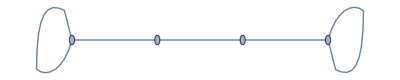

{1/2 (-1-√5),1/2 (1+√5),1/2 (1-√5),1/2 (-1+√5)}

{{1+L/(-1+L^2),1/(-1+L^2)},{1/(-1+L^2),1+L/(-1+L^2)}}

{{1+(1-√5)/(2 (-1+1/4 (1-√5)^2)),1/(-1+1/4 (1-√5)^2)},{1/(-1+1/4 (1-√5)^2),1+(1-√5)/(2 (-1+1/4 (1-√5)^2))}}

{1/2 (5+√5),1/2 (3-√5)}

{{1/2 ⅇ^((2 ⅈ √5 t)/(-1+√5)) (1+ⅇ^(-(4 ⅈ t)/(-1+√5))),1/2 ⅇ^((2 ⅈ √5 t)/(-1+√5)) (-1+ⅇ^(-(4 ⅈ t)/(-1+√5)))},{1/2 ⅇ^((2 ⅈ √5 t)/(-1+√5)) (-1+ⅇ^(-(4 ⅈ t)/(-1+√5))),1/2 ⅇ^((2 ⅈ √5 t)/(-1+√5)) (1+ⅇ^(-(4 ⅈ t)/(-1+√5)))}}

{{0,-ⅇ^(1/2 ⅈ √5 π)},{-ⅇ^(1/2 ⅈ √5 π),0}}

```mathematica
(*Path graph with weighted self=loops on the end has PST per Perfect state transfer in quantum walks on graphs by Kendon*)
(*This one works with 1/2 (1-√5) and 1/2 (-1+√5)*)
P = AdjacencyGraph[{{1,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,1}}]
Eigenvalues[MyAdjacencyMatrix[P]]
Simplify[Smash[P,{1,4}]]
mat = Simplify[Smash[P,{1,4}]] /. L -> 1/2 (1-√5)
Simplify[Eigenvalues[mat]]
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π(-1+√5)/4]
```

```mathematica
(*This one works with 1/2 (-1-√5) and 1/2 (1+√5)*)
P = AdjacencyGraph[{{1,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,1}}]
Eigenvalues[MyAdjacencyMatrix[P]]
Simplify[Smash[P,{1,4}]]
mat = Simplify[Smash[P,{1,4}]] /. L -> 1/2 (1+√5)
Simplify[Eigenvalues[mat]]
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π(1+√5)/4]
```

-Graphics-

{1/2 (-1-√5),1/2 (1+√5),1/2 (1-√5),1/2 (-1+√5)}

{{1+L/(-1+L^2),1/(-1+L^2)},{1/(-1+L^2),1+L/(-1+L^2)}}

{{1+(1+√5)/(2 (-1+1/4 (1+√5)^2)),1/(-1+1/4 (1+√5)^2)},{1/(-1+1/4 (1+√5)^2),1+(1+√5)/(2 (-1+1/4 (1+√5)^2))}}

{1/2 (3+√5),1/2 (5-√5)}

{{1/2 ⅇ^((2 ⅈ √5 t)/(1+√5)) (1+ⅇ^((4 ⅈ t)/(1+√5))),1/2 ⅇ^((2 ⅈ √5 t)/(1+√5)) (-1+ⅇ^((4 ⅈ t)/(1+√5)))},{1/2 ⅇ^((2 ⅈ √5 t)/(1+√5)) (-1+ⅇ^((4 ⅈ t)/(1+√5))),1/2 ⅇ^((2 ⅈ √5 t)/(1+√5)) (1+ⅇ^((4 ⅈ t)/(1+√5)))}}

{{0,-ⅇ^(1/2 ⅈ √5 π)},{-ⅇ^(1/2 ⅈ √5 π),0}}

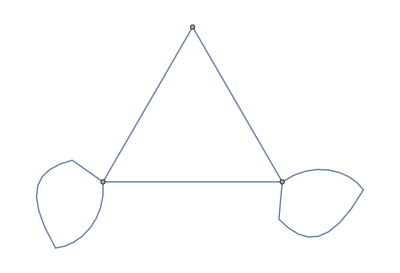

{2,-1,-1}

{{1+1/L,1+1/L},{1+1/L,1+1/L}}

{{3/2,3/2},{3/2,3/2}}

{3,0}

{{1/2 (1+ⅇ^(3 ⅈ t)),1/2 (-1+ⅇ^(3 ⅈ t))},{1/2 (-1+ⅇ^(3 ⅈ t)),1/2 (1+ⅇ^(3 ⅈ t))}}

{{0,-1},{-1,0}}

```mathematica
K = AdjacencyGraph[{{1,1,1},{1,0,1},{1,1,1}}]
Eigenvalues[MyAdjacencyMatrix[K]]
Simplify[Smash[K,{1,3}]]
mat = Simplify[Smash[K,{1,3}]] /. L -> 2
Eigenvalues[mat]
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/3]
```